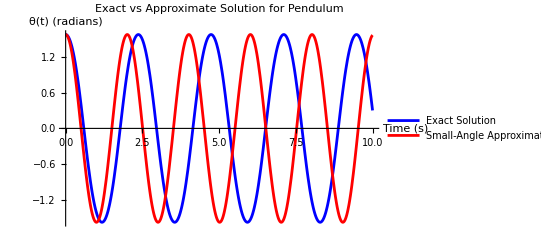

```mathematica
g=9.8; (*acceleration due to gravity in m/s^2*)
l=1;   (*length of the pendulum in meters*)
θ0=Pi/2;  (*initial angular displacement in radians (45 degrees)*)

(*Exact solution without small-angle approximation*)
exactSolution=NDSolve[{θ''[t]+(g/l) Sin[θ[t]]==0,θ[0]==θ0,θ'[0]==0},θ,{t,0,10}];

(*Approximate solution with small-angle approximation*)
approxSolution=NDSolve[{θ''[t]+(g/l) θ[t]==0,θ[0]==θ0,θ'[0]==0},θ,{t,0,10}];

(*Plot both solutions on the same graph*)
Plot[{θ[t]/. exactSolution,θ[t]/. approxSolution},{t,0,10},PlotRange->All,PlotStyle->{Blue,Red},PlotLabel->"Exact vs Approximate Solution for Pendulum",AxesLabel->{"Time (s)","θ(t) (radians)"},PlotLegends->{"Exact Solution","Small-Angle Approximation"}]
```

```mathematica
g=9.8;   (*acceleration due to gravity in m/s^2*)
l=1;     (*length of the pendulum in meters*)

(*Interactive Manipulate for damping and initial angle*)
Manipulate[Module[{exactSolution,approxSolution},(*Exact solution with damping included*)exactSolution=NDSolve[{θ''[t]+c θ'[t]+(g/l) Sin[θ[t]]==0,θ[0]==θ0,θ'[0]==0},θ,{t,0,10}];
(*Approximate solution with small-angle approximation and damping included*)approxSolution=NDSolve[{θ''[t]+c θ'[t]+(g/l) θ[t]==0,θ[0]==θ0,θ'[0]==0},θ,{t,0,10}];
(*Plot both solutions on the same graph*)Plot[{θ[t]/. exactSolution,θ[t]/. approxSolution},{t,0,10},PlotRange->All,PlotStyle->{Blue,Red},PlotLabel->"Exact vs Approximate Solution for Damped Pendulum",AxesLabel->{"Time (s)","θ(t) (radians)"},PlotLegends->{"Exact Solution","Small-Angle Approximation"}]],{{c,0.1},0,1,0.01},(*Slider for damping coefficient*){{θ0,Pi/4},0,Pi/2,0.01}  (*Slider for initial angle in radians*)]
```